8.02 Mathematica Lesson 4
"Open/Close CoSet"

Click Enable Dynamics  in the right upper corner of the notebook before starting to work!

Click Evaluation in the tool bar and then click Evaluate Notebook to evaluate all the variables and the functions in the code that are in the notebook. This will take about 30 seconds. 

After reading this Mathematica notebook, you will be able to: 1)  calculate an integral to obtain the magnetic field using Biot-Savart,  2) calculate derivatives and find maximum and minimum of a function.

Tutorial : The tutorial is divided in three parts. Reading the tutorial and interacting with the pieces of code in it will prepare you to do the problem of the assignment.

Save my work: After typing one or several lines of code in your solution you can click “Save my work and Give Feedback”. “Save my work” does NOT save the changes done in the notebook. It locks your answer into the notebook by creating gray cells that can not be edited anymore. If you are not pleased with your answer you will be able to type a new solution as many times as you want.  

Access Solution: Note that after clicking “Save my work and Give Feedback” for the first time you will be able to view the solution.  This is done for pedagogical purposes. There are many ways of writing a code so the posted solution might be different from yours. 

Save: Before closing the notebook make sure that you have saved your changes by clicking Save from the File menu. If you do not save the changes the grader will not see your work and you will not receive a grade.  (Saving a file frequently is always  a good practice!)

Upload to Stellar: Do not forget to upload your notebook to Stellar!!

graphics initialization (modifying options)

(*we probably won't need these*)
(*r=1.7;
radius = .04(*.4*);
inradius = .05;
radiusTWO = .1;
outerchg =2;*)
Clear[x,y,z];
Clear[PointChargeAtOriginField,x,y,z,charg];

(*changing default options for ContourPlot3D. We could even modify the d.v.'s i*)
Unprotect[ContourPlot3D];
Options[ContourPlot3D]=
{
	(*modified options*)
	PlotPoints→(*17*)26,(*Mesh→All,*)MaxRecursion→0,Mesh→None,
	ColorFunction→"TemperatureMap",ViewPoint→{1.3,-2.4,-31.}(*need to use ViewMatrix*),Contours→Range[-7,7],
	
	(*original options*)
	AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→"Fit",SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision
};
Protect[ContourPlot3D];

Unprotect[ContourPlot];
Options[ContourPlot]=
{
	(*modified options*)
	ContourLabels→True,Contours→16,
	
	(*original options*)
	Sequence@@Options[ContourPlot]
};
Protect[ContourPlot];

(*Unprotect[SliceVectorPlot3D];
Options[SliceVectorPlot3D]=
{
	(*original options*)
	Sequence@@Options[SliceVectorPlot3D],
	
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{.1,.1,-10},VectorScale→{Medium, 0.6, (*Sqrt@*)Sqrt[#5]&(*Automatic*)},(*Boxed→False,*)
	Axes→True, PlotStyle→Opacity[0.1],VectorPoints→17(*RandomReal[{-2,2},{2,888}]*),AxesLabel→Automatic
};
Protect[SliceVectorPlot3D];*)
SetOptions[SliceVectorPlot3D,ViewPoint→{.1,.1,10}];
SetOptions[SliceVectorPlot3D,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}];
SetOptions[SliceVectorPlot3D,Axes→True];
SetOptions[SliceVectorPlot3D,PlotStyle→Opacity[0.1]];
SetOptions[SliceVectorPlot3D,VectorPoints→16];
SetOptions[SliceVectorPlot3D,AxesLabel→Automatic];
SetOptions[SliceVectorPlot3D,ImageSize→Large];
SetOptions[SliceVectorPlot3D,VectorStyle→Arrowheads[.01]];

SetOptions[VectorPlot,VectorStyle→Arrowheads[.02]];
SetOptions[VectorPlot,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2)^.3&(*Automatic*)}];
SetOptions[VectorPlot,VectorPoints→16];

Unprotect[VectorPlot3D];
Options[VectorPlot3D]=
{
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{11,-20,4}(*need to use ViewMatrix!*),VectorScale→{Automatic,Automatic,Function[If[1/(#1^2+#2^2+#3^2)>2,None,1/(#1^2+#2^2+#3^2)]]}(*{Small, .6, (*Sqrt@*)(*1/*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}*),(*Boxed→False,*)
Axes→True, (*PlotStyle→Opacity[0.3],*)VectorPoints→10(*RandomReal[{-2,2},{2,888}]*),AxesLabel→{"x","y","z"},
	(*original options*)
	Sequence@@Options[VectorPlot3D]
};
Protect[VectorPlot3D];
SetOptions[VectorPlot3D,ImageSize→Large];

Clear[x,y,z];

Magnetic field produced by a ring
"Open/Close Chapter"

Derivatives in the Wolfram Language
"Open/Close Section"

To compute most derivatives in the Wolfram Language (including partial derivatives)  the built-in function to use is D[ ]. 

The first argument you must give to D[ ] is the function you want to differentiate, and the second argument is the variable(s) with respect to which you want to take the derivative. For example, for a function “f” we define ourselves:

f[x_]:=-3(x-2)^2

To take the derivative of f with respect to x, we would evaluate:

D[f[x],x]

-6 (-2+x)

To evaluate this derivative at the point x = 5, we first find the derivative in terms of x, then simple replace x with 5 in that expression. To replace the variable x by the value 5 we use the symbol “./ “ (short for ReplaceAll ) and type   /.x→ 5

D[f[x],x]/.x→5  (* exaluate the derivative at x = 5 using /.x → 5 *)

-18

Maximum of a function: To find a (local) maximum of the function we can use FindMaximum[ ].

FindMaximum[f[x], {x,0.3}]

{0.,{x→2.}}

Input:
The arguments of FindMaximum[ ] are two. The first one is the function we wish to find a maximum of, the second is a list with two elements: the  function’s independent variable and  an initial value of x at which FindMaximum will start to look for the local maximum.  
In this example the second argument is the list  {x, 0.3}, where 0.3 is the starting point. 
Output:
The output of FindMaximum[ ] is a list of two elements:
The first element is the maximum value of f[x] (zero in this case)
The second element, “x -> 2” is the value of x at which f[x]  achieves a local maximum.

Note 1: To find a local minimum of a function use FindMinimum[ function,  {x,xo}]  where xo is the starting point.

Note 2: Be aware that both functions, FindMaximum[] and findMinimum[],  do not always give the answer at the first trial.  It depends on the given value of the starting point xo, If we use an xo close to the maximum or minimum both functions will give you the proper answer.

To extract the value of 2 from the output of FindMaximum[ ] we type the following line:

x/.Last[FindMaximum[f[x], {x,0.3}]]

2.

Note: 

1. Last[ ] is a function that returns the last element of a list:

 Example: Last[ {1, 2, 4, 0, -3} ] returns -3. Therefore, Last[ FindMaximum[ f[x], {x,0.3} ] ] returns {x -> 2.} 

2. the symbol  “/.”  (short for ReplaceAll) is used to replace the variable x by the the value of 2

Plot f[x] vs x using the Plot[ ] function:

Plot[f[x],{x,-3,3}]

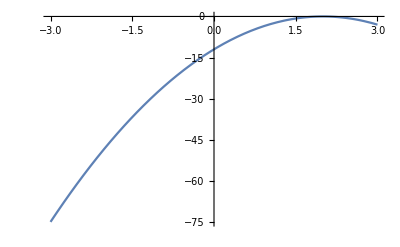

Note: The second argument has the same form as the plot range arguments of VectorPlot, StreamPlot, etc.: {x, -3, 3} instructs  Plot[ ]  to plot f[x] on the range -3 < x < 3.

Vector product in  the Wolfram Language
"Open/Close Section"

To calculate the vector product, or cross product, between two vectors we use the function Cross[ ].:

Cross[ A⃗, B⃗ ] =  A⃗  x  B⃗

Example: do the cross product between î and ĵ to obtain k̂

Cross[{1,0,0},{0,1,0}]

{0,0,1}

Note: The input vectors must have three components.
If we use  î = { 1, 0 }   and   ĵ = {0, 1} the function Cross[ ] returns an error message.

Calculate the Magnetic Field of a ring along the ring’s axis.
"Open/Close Section"

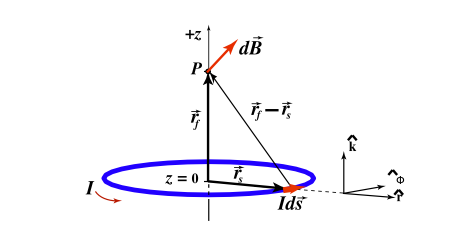
In this section we will calculate the magnetic field at a generic point P in the axis of a ring of radius a. Set the z-axis to be the axis of symmetry of the ring . 
                                       
                                                                       -Graphics-
Consider the element of current Id s⃗ shown in the figure. The magnetic field produced by  Id s⃗ at a point P in the axis of the ring is given by the Biot-Savart’s law:

                                       (eq. 1)

where  (r⃗)_f is the field point, position of point P,  and  (r⃗)_s is the source point, the position of the element of current  Id s⃗ in the ring.  In the piece of code below we define the function dB that calculates the infinitesimal magnetic field  d B⃗   given in (eq. 1).

muo = 4*Pi * 10^(-7) ; (* permeabilty in free space T.m/A *)

dB[sourcePoint_, fieldPoint_,ids_] := 
 (muo/4*Pi)*Cross[ids,(fieldPoint-sourcePoint )]/EuclideanDistance[fieldPoint, sourcePoint]^3

The arguments of the dB[ ] function are defined below:

If ϕ is the angular variable in cylindrical coordinates ( 0 < ϕ <2π ).

1. “sourcePoint” or (r⃗)_s   is  along the r-hat direction. 

Because r̂ = cos(ϕ)î+ a sin(ϕ)ĵ⟹ 
               (r⃗)_s = a cos(ϕ)î+ a sin(ϕ)ĵ  ⟹   
               sourcePoint = { aCos[phi], aSin[phi], 0}


2.  “fieldPoint”  or (r⃗)_f  is  in the z-axis: 

(r⃗)_f = z k̂      ⟹   fieldPoint = {0, 0, z}


3. “Ids”  or Id s⃗  is in the phi-hat direction (tangent to the ring). 

Because ϕ̂ = -sin(ϕ)î+ cos(ϕ)ĵ and ds = a dϕ  ⟹ 

               I d s⃗ = I  * (a dϕϕ̂) =I a dϕ (- sin(ϕ) î+ cos(ϕ) ĵ ) ⟹

               Ids =  current * { -aSin[phi],  aCos[phi], 0}  dϕ

Note: we will not include dϕ in the argument of dB[ ] because  dϕ is already considered in Integrate[ ]

To calculate the magnetic field at any point  in the z-axis we need to integrate (eq. 1) over the ring:
                                      (eq. 2)
We will use the  Integrate[ ] function to integrate the function dB[ ] with respect to phi (0, 2Pi) as shown below:

current= 10^(-3) ; (* current in amperes A*)
a =0.3;   (* ring radius in m*)

bField = Integrate[
dB[{a Cos[phi],a Sin[phi],0},{0,0,z},current * {-a Sin[phi],a Cos[phi],0}], {phi,0,2Pi},
Assumptions→ Element[z,Reals]
]

{0.,0.,(5.58113×10^-7)/((9.+100. z^2)^(3/2))}

Note: 
1. We did not include dϕ in the third argument of dB[ ] because  dϕ  is already considered in Integrate[ ]

2. This is the magnetic field at any point along the z-axis. 

3. As discussed in class,  the magnetic field has only a z-component due to the axial symmetry of the problem.

The z-component of the magnetic field can be obtained doing the “dot” product between the magnetic field and k̂ :   B_z = B⃗.k̂  . 

Note:  To obtain the z-component of the electric field we can also use:
Last[bField],  bField[[3]]   or  bField[[-1]]

The line of code below calculates the z-component of the magnetic field along the z-axis:

bFieldz =  bField . {0,0,1};    (*  B_z = B⃗.k̂  (dot product) *)

Plot[bFieldz, {z, -2, 2}, PlotRange→Full]

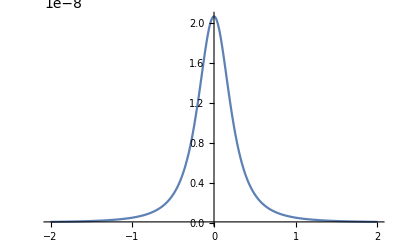

Note that we have used in the Plot[ ] function the option  “PlotRange→Full”. This option uses the full range of z to plot the function. This is because, when the radius of the ring is smaller than one, Plot[] chooses not to plot the “bFieldz” function for the values of z close to zero. Using PlotRange->Full we are able to see the complete plot.  (Try Plot[bFieldz, {z, -2, 2}] without the PlotRange option and you will see a truncated plot!!!!!)

The plot shows a symmetric z-component of the B-field with respect to z=0, with a maximum at z = 0. We can check this using FindMaximum[ ]

FindMaximum[bFieldz,{z,.3}]

{2.06709×10^-8,{z→2.38778×10^-11}}

The second element of the output list of FindMaximum[] is {z→2.38778×10^-11} , which is approximately zero as expected

Calculate the derivative of the z-component of the electric field.

derivativeBz = D[bFieldz,z];
Plot[derivativeBz , {z,-3,3}, PlotRange→Full]

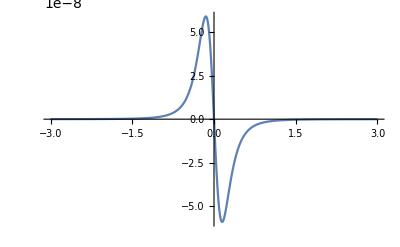

The plot of the derivative of the z-component of the B-field shows a maximum and a minimum.

Find the location of the maximum:

zmax= z/. Last[FindMaximum[derivativeBz,{z,0}]]

-0.15

In the line of code above there are three operations involved:

1. Find the local  maximum starting at z = 0 using FindMaximum[ derivativeBz, {z,0} ].

2. Extract the last element of the output list calculated by FindMaximum[ ] using  Last[ FindMaximum[ derivativeBz, {z,0} ] ].

3. Assigned the value of -0.15 to zmax using  zmax = z /. Last[ FindMaximum[ derivativeBz, {z,0} ] ]

Similarly we find the location of the minimum as follows:

zmin= z/. Last[FindMinimum[derivativeBz,{z,0}]]

0.15

Problem - Helmholtz Coils
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

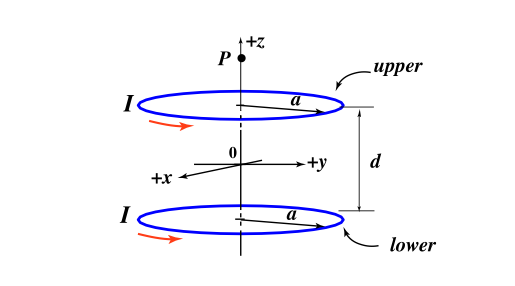
Consider two parallel rings of radius a = 0.15 m, with a current  I = 3 mA. The rings are separated by a distance d = a. Each ring consists of 200 turns of a thin conducting wire. The current circulates counterclockwise as viewed from above on the + z-axis. Consider the zero of the coordinate system to be the midpoint between the two rings as shown in the figure.

                                        -Graphics-


i.   Calculate the z-component of the magnetic field at any point along the z-axis and plot it vs. z.

ii.  Plot the derivative of the z-component of the magnetic field, plot it vs. z, and calculate its value at z = 0,     ( dB_z/dz = ?  at  z=0)

iii.  Plot the second derivative of the z-component of the magnetic field vs. z,  and calculate its value at z = 0.    ( (d^2 B_z)/dz^2 = ?  at  z=0)

v. At what values of z is the first derivative of the z-component of the magnetic field a maximum or a minimum? Compare those values with the radius of the ring a = 0.15 m.

Work saved at Sat 17 Mar 2018 11:35:20

```mathematica
currentNew= 10^(-3) ; (* current in amperes A*)
aNew =0.15;   (* ring radius in m*)
d = aNew; (* ring separation in m*)

bFieldNewTop = Integrate[
dB[{aNew Cos[phi],aNew Sin[phi],0},{0,0,z-(d/2)},200*currentNew * {-aNew Sin[phi],aNew Cos[phi],0}], {phi,0,2Pi},
Assumptions-> Element[z,Reals]
]
```

{0.,0.,0.000159741/((9.-48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewBottom = Integrate[
dB[{aNew Cos[phi],aNew Sin[phi],0},{0,0,z+(d/2)},200*currentNew * {-aNew Sin[phi],aNew Cos[phi],0}], {phi,0,2Pi},
Assumptions-> Element[z,Reals]
]
```

{0.,0.,0.000159741/((9.+48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewTotal = bFieldNewTop+bFieldNewBottom
```

{0.,0.,0.000159741/((9.-48. z+320. z^2)^(3/2))+0.000159741/((9.+48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewZ = bFieldNewTotal.{0,0,1}
```

0.+0.000159741/((9.-48. z+320. z^2)^(3/2))+0.000159741/((9.+48. z+320. z^2)^(3/2))

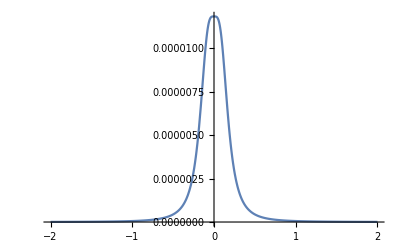

```mathematica
Plot[bFieldNewZ,{z,-2,2},PlotRange->All]
```

```mathematica
FirstDerivativeBFieldNewZ = D[bFieldNewZ,z]
```

-(0.000239612 (-48.+640. z))/((9.-48. z+320. z^2)^(5/2))-(0.000239612 (48.+640. z))/((9.+48. z+320. z^2)^(5/2))

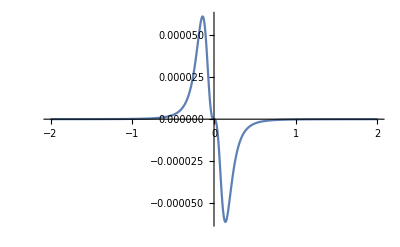

```mathematica
Plot[FirstDerivativeBFieldNewZ, {z,-2,2},PlotRange->All]
```

```mathematica
FirstDerivativeBFieldNewZ/.z->0
```

0.

```mathematica
SecondDerivativeBFieldNewZ = D[FirstDerivativeBFieldNewZ,z]
```

(0.00059903 (-48.+640. z)^2)/((9.-48. z+320. z^2)^(7/2))-0.153352/((9.-48. z+320. z^2)^(5/2))+(0.00059903 (48.+640. z)^2)/((9.+48. z+320. z^2)^(7/2))-0.153352/((9.+48. z+320. z^2)^(5/2))

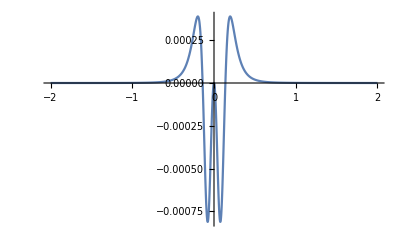

```mathematica
Plot[SecondDerivativeBFieldNewZ, {z,-2,2},PlotRange->All]
```

```mathematica
SecondDerivativeBFieldNewZ/.z->0
```

0.

```mathematica
FindMinimum[FirstDerivativeBFieldNewZ,{z,0.01}]
```

{-0.0000611447,{z→0.139355}}

```mathematica
FindMaximum[FirstDerivativeBFieldNewZ,{z,-0.01}]
```

{0.0000611447,{z→-0.139355}}

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
currentNew= 10^(-3) ; (* current in amperes A*)
aNew =0.15;   (* ring radius in m*)
d = aNew; (* ring separation in m*)

bFieldNewTop = Integrate[
dB[{aNew Cos[phi],aNew Sin[phi],d/2},{0,0,z},200*currentNew * {-aNew Sin[phi],aNew Cos[phi],0}], {phi,0,2Pi},
Assumptions-> Element[z,Reals]
]
```

{0.,0.,0.000159741/((9.-48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewBottom = Integrate[
dB[{aNew Cos[phi],aNew Sin[phi],-d/2},{0,0,z},200*currentNew * {-aNew Sin[phi],aNew Cos[phi],0}], {phi,0,2Pi},
Assumptions-> Element[z,Reals]
]
```

{0.,0.,0.000159741/((9.+48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewTotal = bFieldNewTop+bFieldNewBottom
```

{0.,0.,0.000159741/((9.-48. z+320. z^2)^(3/2))+0.000159741/((9.+48. z+320. z^2)^(3/2))}

```mathematica
bFieldNewZ = bFieldNewTotal.{0,0,1}
```

0.+0.000159741/((9.-48. z+320. z^2)^(3/2))+0.000159741/((9.+48. z+320. z^2)^(3/2))

```mathematica
Plot[bFieldNewZ,{z,-2,2},PlotRange->All]
```

-Graphics-

```mathematica
FirstDerivativeBFieldNewZ = D[bFieldNewZ,z]
```

-(0.000239612 (-48.+640. z))/((9.-48. z+320. z^2)^(5/2))-(0.000239612 (48.+640. z))/((9.+48. z+320. z^2)^(5/2))

```mathematica
Plot[FirstDerivativeBFieldNewZ, {z,-2,2},PlotRange->All]
```

-Graphics-

```mathematica
FirstDerivativeBFieldNewZ/.z->0
```

0.

```mathematica
SecondDerivativeBFieldNewZ = D[FirstDerivativeBFieldNewZ,z]
```

(0.00059903 (-48.+640. z)^2)/((9.-48. z+320. z^2)^(7/2))-0.153352/((9.-48. z+320. z^2)^(5/2))+(0.00059903 (48.+640. z)^2)/((9.+48. z+320. z^2)^(7/2))-0.153352/((9.+48. z+320. z^2)^(5/2))

```mathematica
Plot[SecondDerivativeBFieldNewZ, {z,-2,2},PlotRange->All]
```

-Graphics-

```mathematica
SecondDerivativeBFieldNewZ/.z->0
```

0.

```mathematica
FindMinimum[FirstDerivativeBFieldNewZ,{z,0.01}]
```

{-0.0000611447,{z→0.139355}}

```mathematica
FindMaximum[FirstDerivativeBFieldNewZ,{z,-0.01}]
```

{0.0000611447,{z→-0.139355}}

Solution 
"Open/Close Section""Access Solution"

i.   Calculate the z-component of the magnetic field at any point along the z-axis and plot it vs. z

Use the bField[ ] function of the tutorial to calculate the fields of both rings and then add them together to answer the questions. Recall that now the origin of the coordinate system is not at the center of the rings.

(* Magnetic Field of the Upper Ring *)
n = 200;  (* number of turns *)
current= 3*10^(-3) ; (* current in amperes A*)
a =0.15;   (* ring radius in m*)
d = a;         (* rind separation *)
bFieldUpper= Integrate[
dB[{a Cos[phi],a Sin[phi],d/2},{0,0,z},current * {-a Sin[phi],a Cos[phi],0}], {phi,0,2Pi},
Assumptions→ Element[z,Reals]
];

Note that the sourcePoint, the position of the element of current, is at a distance d/2 above the zero of the coordinate system, therefore the z-component is +d/2 instead of zero: 

sourcePoint = { a Cos[phi], a Sin[phi],  d/2 }

(* Magnetic Field of the Lower Ring *)
bFieldLower= Integrate[
dB[{a Cos[phi],a Sin[phi],-d/2},{0,0,z},current *{-a Sin[phi],a Cos[phi],0}], {phi,0,2Pi},
Assumptions→ ( Element[z,Reals])
];

Note that the sourcePoint, the position of the element of current, is at a distance d/2 below the zero of the coordinate system, therefore the z-component is -d/2 instead of zero:

sourcePoint = { a Cos[phi], a Sin[phi], - d/2 }

The total magnetic field is given by the sum of bFieldUpper[] + bFieldLower[]

(* The total magneticg field *)
bFieldTotal = bFieldUpper + bFieldLower; (* superposoition *)
bFieldTotalz = bFieldTotal . {0, 0, 1}; (* the z-component*)
Plot[bFieldTotalz, {z,-.5, .5}]

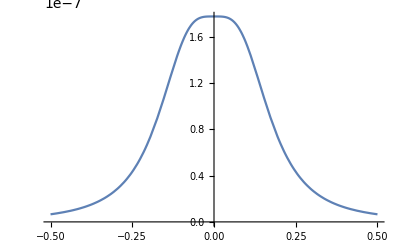

Note that the z-component of the magnetic field is almost constant around z = 0, we expect the derivative of the z-component to be zero at z = 0. You will check this by answering the question (ii).

ii.  Calculate the derivative of the z-component of the magnetic field, plot it vs. z, and calculate its value at z = 0,     ( dB_z/dz = ?  at  z=0)
 
Use the function D[ ] to calculate the derivative of  “bFieldTotalZ”,  use Plot[ ] to plot it.,  and use /.z→0 to evaluate the derivative at z = 0.

(*Calculate dB_z/dz:  *)
firstDeriv =D[ bFieldTotalz, z];  

(*Plot dB_z/dz vs z: *)
Plot[firstDeriv, {z,-.5,.5}]         

(* Calculate dB_z/dz at z=0:  *)
firstDerivAtZero = firstDeriv/.z→0 ;  (* use /.z→0 replaces z by 0 in the expression of "firstDeriv*)

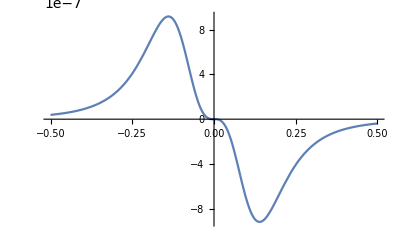

From the plot, we observe that the derivative of the z-component of the B-filed is zero at  z = 0.  Check it with the value of “firstDerivAtZero”  calculated in the third line of the code above.  

Note that the first derivative is also flat around zero. As a result, we expect the second derivative of the B-field to be zero around z = 0. You will check this by answering question (iii).

The plot shows a maximum and a minimum of the first derivative of the z-component of the B-field. You will calculate those points by answering question  (iv).

iii.  Plot the second derivative of the z-component of the magnetic field vs. z,  and calculate its value at z = 0.    ( (d^2 B_z)/dz^2 = ?  at  z=0)
Use the function D[ ] to calculate the derivative of  “firstDeriv”,  use Plot[ ] to plot it, and use /.z→0 to evaluate the second derivative at z =0.

(*Calculate second derivative:*)
secondDeriv =D[ firstDeriv , z];   

(* Plot th e second derivative vs. z :*)
Plot[secondDeriv , {z,-.5,.5}]  

(* Calculate second derivative at z=0:*) 
secondDerivAtZero = secondDeriv /.z→0 ; (*/.z→0 replaces z by 0 *)

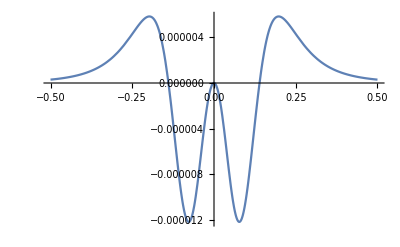

From the plot we can see that the second derivative of the z-component of the B-field is zero at  z = 0.  Check if the value “secondDerivAtZero” in the third line of code above is zero.

v. At what values of z is the first derivative of the z-component of the magnetic field a maximum or a minimum? Compare those values with the radius of the ring a = 0.15 m. 

Use FindMaximum[ ] and FindMinimum[] to calculate the value(s) of z for which “firstDeriv” is a maximum or a minimum. Use as starting points values of z close to the local maximum and minimum. You can get those values looking at the plot of “firstDeriv”.

zmax1 = z/.Last[ FindMaximum[firstDeriv, {z, -0.4}]]
zmin1 = z/.Last[ FindMinimum[firstDeriv, {z, 0.4}]]

-0.139355

0.139355

Due to the symmetry of the B-field  the magnitudes of zmax1 and zmin1 are the same. 

Considering that  the radius of each ring is a = 0.15 m, the location of the maximum and minimum of the first derivative of the B-field is approximately at  z ~ -a  and z ~ a. As a result, a little bar magnet place at these values of z will experience the largest force.  (Recall that F ~ dBz/dz, section 8.4.1).

(*Plot the three functions in the same figure: the z-component of the field its first and second derivatives *)

Plot[{bFieldTotalz,firstDeriv, secondDeriv }, {z,-.5,.5},PlotRange→Full, PlotTheme→"Detailed"]

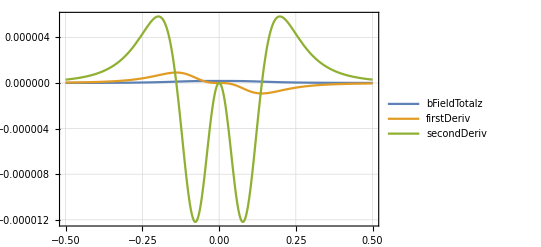

Use the button above to start viewing the solution